## Physics 449 hw#4 due Mar 16 W8F

Name: Ruojun Wang
Date: 3/11 W8Sun

```mathematica
<<"http://www.physics.wisc.edu/~tgwalker/448defs.m"
```

## 1-2)

### Look up the function ξ(r) in the spin-orbit Hamiltonian H_SO=ξ(r)L·S for hydrogen. Be sure to write it in atomic units.

H=H_0+H_SO

B = (2 μ_B L)/r^3
H_SO=2 μ_B S·B= (2 μ_B^2 S·L)/r^2 = (2 S·L)/r^2 ((e ℏ)/(2m c))^2
ξ = (2 μ_B^2)/(r^2 a_B^3)=1/(2 r^2 a_B^3)((e ℏ)/(m c))^2
L·S=(j(j+1)-l(l+1)-s(s+1))/2=Piecewise[{{1/2, j=3/2}, {-1, j=1/2}}]

Rescaling the Hamiltonian: 
H=(-1/2∂_s^2 +((l(l+1))/(2 s^2)-1/s))+1/(2 s^3 a_0 m)(e/c)^2 S·L
α = e^2/ℏc=1/137
H=(-1/2∂_s^2 +((l(l+1))/(2 s^2)-1/s))+(α^2 mc^2)/(2 s^3 m)(1/c)^2 S·L
H=(-1/2∂_s^2 +((l(l+1))/(2 s^2)-1/s))+α^2/(2 s^3)S·L

### Calculate the matrix H_0+H_SO using the 2p...5p P_j states as a basis.

```mathematica
Subscript[P, n_,l_,z_][r_]:=√z Subscript[P, n,l][z r];
n = Range[2,6];
```

```mathematica
Hso1=Table[Integrate[1/r^3 Subscript[P, n1,1,1][r]Subscript[P, n2,1,1][r],{r,0,∞}],{n1,n},{n2,n}]//FullSimplify
```

{{1/24,-8/375,7/(162 √10),-1096/(50421 √5),67/(1536 √35)},{-8/375,1/81,-(628 √(2/5))/50421,77/(6144 √5),-4456/(177147 √35)},{7/(162 √10),-(628 √(2/5))/50421,1/192,-(12508 √2)/4782969,24601/(2343750 √14)},{-1096/(50421 √5),77/(6144 √5),-(12508 √2)/4782969,1/375,-37814408/(7073843073 √7)},{67/(1536 √35),-4456/(177147 √35),24601/(2343750 √14),-37814408/(7073843073 √7),1/648}}

```mathematica
Hso1//N//MatrixForm
```

(0.0416667 | -0.0213333 | 0.0136642 | -0.00972107 | 0.00737309
-0.0213333 | 0.0123457 | -0.00787731 | 0.00560473 | -0.00425184
0.0136642 | -0.00787731 | 0.00520833 | -0.00369833 | 0.00280529
-0.00972107 | 0.00560473 | -0.00369833 | 0.00266667 | -0.00202047
0.00737309 | -0.00425184 | 0.00280529 | -0.00202047 | 0.00154321)

```mathematica
Eso1 = -1/(2 n^2); α = 1/137;
```

when j=3/2,L·S=1/2

```mathematica
H1a = DiagonalMatrix[Eso1] + α^2/4 Hso1//FullSimplify//N;H1a//MatrixForm
```

(-0.124999 | -2.84156×10^-7 | 1.82004×10^-7 | -1.29483×10^-7 | 9.82084×10^-8
-2.84156×10^-7 | -0.0555554 | -1.04925×10^-7 | 7.46541×10^-8 | -5.66339×10^-8
1.82004×10^-7 | -1.04925×10^-7 | -0.0312499 | -4.92611×10^-8 | 3.7366×10^-8
-1.29483×10^-7 | 7.46541×10^-8 | -4.92611×10^-8 | -0.02 | -2.69124×10^-8
9.82084×10^-8 | -5.66339×10^-8 | 3.7366×10^-8 | -2.69124×10^-8 | -0.0138889)

```mathematica
evalH1a = Eigenvalues[H1a]
```

{-0.124999,-0.0555554,-0.0312499,-0.02,-0.0138889}

when j=1/2, L·S=-1

```mathematica
H1b = DiagonalMatrix[Eso1] - α^2/2 Hso1//FullSimplify//N;H1b//MatrixForm
```

(-0.125001 | 5.68313×10^-7 | -3.64009×10^-7 | 2.58966×10^-7 | -1.96417×10^-7
5.68313×10^-7 | -0.0555559 | 2.09849×10^-7 | -1.49308×10^-7 | 1.13268×10^-7
-3.64009×10^-7 | 2.09849×10^-7 | -0.0312501 | 9.85222×10^-8 | -7.4732×10^-8
2.58966×10^-7 | -1.49308×10^-7 | 9.85222×10^-8 | -0.0200001 | 5.38247×10^-8
-1.96417×10^-7 | 1.13268×10^-7 | -7.4732×10^-8 | 5.38247×10^-8 | -0.0138889)

```mathematica
evalH1b= Eigenvalues[H1b]
```

{-0.125001,-0.0555559,-0.0312501,-0.0200001,-0.0138889}

### Find the 2p P_(3/2)-2p P_(1/2) energy splitting. Compare to what you get by simply calculating ⟨H_SO⟩ and subtracting.

```mathematica
evalH1a⟦1⟧-evalH1b⟦1⟧
```

1.66498×10^-6

```mathematica
(* ⟨Subscript[H, so]⟩ *)

Hso1Exp=α^2/2 Hso1⟦1,1⟧ *(1/2+1)//N
```

1.66498×10^-6

The 2p P_(3/2)-2p P_(1/2) energy splitting agrees with the value by simply calculating ⟨H_SO⟩ and subtracting.

## 3)

(on the hand written page)

## 4) T 11.5-

### a) The exact energy states

```mathematica
$Assumptions={A>0,μE>0};
```

```mathematica
Hammo={{μE, A}, {A, -μE}};{evalHa,eveHa1}=Eigensystem[Hammo]//Simplify;

eveHa2a=Normalize/@eveHa1//FullSimplify;
eveHa2=eveHa1/. μE ->0//Simplify
eveHa=Normalize/@eveHa2//FullSimplify
```

{{-1,1},{1,1}}

{{-1/(√2),1/(√2)},{1/(√2),1/(√2)}}

ψ_n=φ_n^0+λ∑_(k≠n) φ_k^0(φ_k^0(Ĥ)_1 φ_n^0)/(E_n^0-E_k^0)+𝒪(λ^2)

```mathematica
ψ1=eveHa⟦1⟧+eveHa⟦2⟧(eveHa⟦2⟧.{{μE, 0}, {0, -μE}}.eveHa⟦1⟧)/(evalHa⟦1⟧-evalHa⟦2⟧)
```

{1/(√2)-μE/(2 √2 A),1/(√2)+μE/(2 √2 A)}

```mathematica
ψ2=eveHa⟦2⟧+eveHa⟦1⟧(eveHa⟦1⟧.{{μE, 0}, {0, -μE}}.eveHa⟦2⟧)/(evalHa⟦2⟧-evalHa⟦1⟧)
```

{-1/(√2)-μE/(2 √2 A),1/(√2)-μE/(2 √2 A)}

### b) The first-order correction

```mathematica
Series[eveHa2a,{μE,0,1}]// PowerExpand
```

{{-1/(√2)+μE/(2 √2 A)+O[μE]^2,1/(√2)+μE/(2 √2 A)+O[μE]^2},{1/(√2)+μE/(2 √2 A)+O[μE]^2,1/(√2)-μE/(2 (√2 A))+O[μE]^2}}

It agrees with the results in a)

## 5) T 11.7

### a)

By Gauss’s Law, ∮ E·ⅆa=Q_encl/ε_0
r>R, E=-e/R(in Gaussian units)→ V(r)=-∫_∞^r E·ⅆl=-∫_∞^r -e/R·ⅆl=-e^2/R
r<R, E=-(3e)/R^2 r/R→ V(r)=-∫_∞^r E·ⅆl=-∫_R^r -(3e)/R^2r/R·ⅆl=e (((3e)/R^2 r/R-(3e)/R^2 R/R))=-(3 e^2)/(2 R^3)(R^2-1/3 r^2)

### b)

The wavefunction for the hydrogen atom: (φ_(1,0))^0=(P(r))/r Y_(l,m)=2(Z/a_0)^(3/2)ⅇ^(-Z r/a_0); (φ_(2,1))^0=(P(r))/r Y_(l,m)=1/(√3)(Z/(2 a_0))^(3/2)(Z r)/a_0 ⅇ^(-Z r/2 a_0)
The energy shift for the 1s E_1^1=φ_1^0Vφ_1^0=φ_1^0 e^2/R-(3 e^2)/(2 R^3)(R^2-1/3 r^2)φ_1^0=∫(φ_1^0)^2(e^2/r-(3 e^2)/(2R)+(e^2 r^2)/(2 R^3))r^2 ⅆrⅆΩ≈^(R<<a_0)4π (φ_1^0)^2∫(e^2/r-(3 e^2)/(2R)+(e^2 r^2)/(2 R^3))r^2 ⅆr

To find the energy shift for 1s:

```mathematica
E1n1=4π*φ1^2*Integrate[((e^2 r^2)/(2 R^3)+e^2/r-(3 e^2)/(2R))r^2,{r,0,R}]
```

2/5 e^2 π R^2 φ1^2

```mathematica
Limit[ (Subscript[P, 1,0][s])/(s √(a0^3))1/(√(4π)),s->0]//FullSimplify
```

1/(√(a0^3) √π)

```mathematica
E1n1b=2/5 e^2 π R^2 (1/(√(a0^3) √π))^2//FullSimplify
```

(2 e^2 R^2)/(5 a0^3)

Plug in e^2→14.4 eV Å, R→1.2×10^-5 Å,a_0→0.5292 Å

```mathematica
(2 (14.4 eV Å)* (1.2*10^-5 Å)^2)/(5 (0.5292 Å)^3)//FullSimplify
```

5.59662×10^-9 eV

To find energy shift for 2p:

```mathematica
Integrate[((e^2 r^2)/(2 R^3)+e^2/r-(3 e^2)/(2R))((r/a0)^2/(√(24 a0)))^2,{r,0,R}]//Simplify
```

(e^2 R^4)/(1120 a0^5)

Plug in e^2→14.4 eV Å, R→1.2×10^-5 Å,a_0→0.5292 Å

```mathematica
((14.4 eV Å)(1.2×10^-5 Å)^4)/(1120 (0.5292 Å)^5)//Simplify
```

6.42348×10^-21 eV

E_1^1=5.59662×10^-9 eV; E_2^1=6.42348×10^-21 eV→E_2^1-E_1^1= -6.42348×10^-21 eV+5.59662×10^-9 eV=5.59662×10^-9 

This shift has little effect on the Lyman α wavelength.

```mathematica
-6.423478517795335*^-21 eV+5.596615474774708*^-9 eV
```

5.59662×10^-9 eV

## 6) Use appropriate Clebsch-Gordan coefficients to calculate the g_j factors for a ^2 D_j state.

^2 D_j: 2 → (2s +1=l)→ 2s+1 =2, D→d-state → l=2, need to find j.
So :   s =_-^+1/2; l =2;
The total angular momentum is the sum of the spin and orbital angular momentum:
j=s+l=1/2+2=5/2   &  j =s+l=-1/2+2=3/2; m = 5/2 or 3/2

To find the expectation value of J_z:

m_j⟨J_z⟩=⟨L_z+2 S_z⟩=m_j((⟨L·S⟩ + l(l+1)+2⟨L·S⟩+2s(s+1))/(j(j+1)))
m_j 5/2=3 
m_j=6/5=g_i

For j=5/2 & m=5/2: 
	j m_j=Cl s→ 5/2 5/2=C2 1/2
	
⟨L_z+2 S_z⟩=m_j((⟨L·S⟩ + l(l+1)+2⟨L·S⟩+2s(s+1))/(j(j+1)))
m_j 5/2 = (2 + (1/2*2)) =(C_(l m_l s m_s)^(j m_s))^2 (3)=1*3=3
m_j=3*2/5=6/5=g_i

```mathematica
ClebschGordan[{2,2},{1/2,1/2},{5/2,5/2}]
```

1

```mathematica
((1+2(2+1)+2(1)+1(3/2))/(5/2(7/2)))//Simplify
```

6/5

∴g_(5/2) factor=6/5

For j=3/2&m=3/2:
There are two possible ways for j & m to be 3/2, l=2 and s=-1/2 or l=1, s=1/2 so the answer will be a combination of the two states.
m_j⟨J_z⟩=⟨L_z+2 S_z⟩=m_j((⟨L·S⟩ + l(l+1)+2⟨L·S⟩+2s(s+1))/(j(j+1)))
m_j 3/2 = (2 + (-1/2*2)) + (1+1)=((C^jm_s)_(lm_l sm_s))^2 (2)+((C^jm_s)_(lm_l sm_s))^2 (2-1)=(1/5)2 +(4/5)1 =6/5
m_j=2/3*6/5=12/15=4/5→ g_i=4/5

j m_j=Cl s
3/2 3/2=C2-1/2+C1 1/2

```mathematica
ClebschGordan[{2,1},{1/2,1/2},{3/2,3/2}]
ClebschGordan[{2,2},{1/2,-1/2},{3/2,3/2}]
```

-1/(√5)

2/(√5)

## 7)

### Calculate the energy levels as a function of magnetic field

s=_-^+1/2, l=2

H_0=A·S·I and V=2 μ_B B ·S_z

```mathematica
s=angmom[1/2];l=angmom[2];
Hso7=2/5 Sum[l⟦p⟧⊗s⟦p⟧,{p,3}];
H7=2/5 Sum[l⟦p⟧⊗s⟦p⟧,{p,3}]+μB A(l⟦3⟧⊗IdentityMatrix[2]+2IdentityMatrix[5]⊗s⟦3⟧);
```

```mathematica
evalHso7= Eigenvalues[Hso7]
```

{-3/5,-3/5,-3/5,-3/5,2/5,2/5,2/5,2/5,2/5,2/5}

```mathematica
{evalH7,eveH7}=Eigensystem[H7];
eveH7=Normalize/@eveH7;
```

```mathematica
evalH7
μB =1;
```

{1/5 (2-15 A),1/5 (2+15 A),1/10 (-1-15 A-√5 √(5-6 A+5 A^2)),1/10 (-1-15 A+√5 √(5-6 A+5 A^2)),1/10 (-1-5 A-√5 √(5-2 A+5 A^2)),1/10 (-1-5 A+√5 √(5-2 A+5 A^2)),1/10 (-1+5 A-√5 √(5+2 A+5 A^2)),1/10 (-1+5 A+√5 √(5+2 A+5 A^2)),1/10 (-1+15 A-√5 √(5+6 A+5 A^2)),1/10 (-1+15 A+√5 √(5+6 A+5 A^2))}

### make a plot showing both the exact results and the approximate answers from 5)

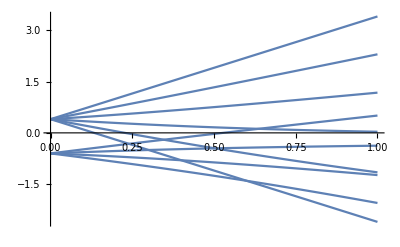

```mathematica
exactRe=Plot[Sort[evalH7],{A,0,1}] (* x:A=(μ B)/Subscript[E, so]=B/(8.72 Gauss);y:E/(h*12.2 MHz)*)
```

The approximate plot:

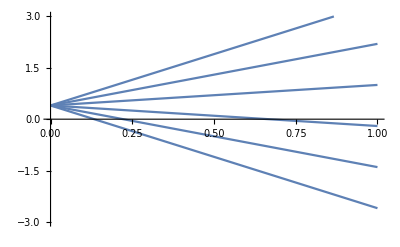

```mathematica
ApproxRe=Plot[2/5+(6/5) A*Range[-5/2,5/2],{A,0,1},PlotRange->{{0,1},{-3,3}}]
```

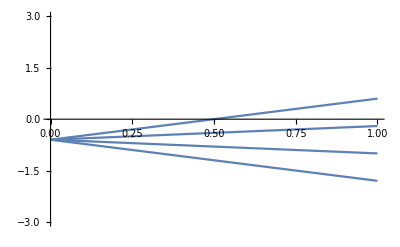

```mathematica
ApproxRe2=Plot[-3/5+(4/5) A*Range[-3/2,3/2],{A,0,1},PlotRange->{{0,1},{-3,3}}]
```